```mathematica
SetDirectory[NotebookDirectory[]];
```

## No Magnetic Field

```mathematica
parentdir="../Processed_Data/11_Appendix_KPM_DOS/No_Magnetic_Field";
```

```mathematica
datadir=StringJoin[parentdir,"/p10q3_ADOS_FullRange_71points"];
```

```mathematica
n7nc512=Import[StringJoin[datadir,"/p10q3n7_Nc512_ADOS.txt"],"Table"];
n7nc1024=Import[StringJoin[datadir,"/p10q3n7_Nc1024_ADOS.txt"],"Table"];
n7nc2048=Import[StringJoin[datadir,"/p10q3n7_Nc2048_ADOS.txt"],"Table"];
n7nc4096=Import[StringJoin[datadir,"/p10q3n7_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n8nc512=Import[StringJoin[datadir,"/p10q3n8_Nc512_ADOS.txt"],"Table"];
n8nc1024=Import[StringJoin[datadir,"/p10q3n8_Nc1024_ADOS.txt"],"Table"];
n8nc2048=Import[StringJoin[datadir,"/p10q3n8_Nc2048_ADOS.txt"],"Table"];
n8nc4096=Import[StringJoin[datadir,"/p10q3n8_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n9nc512=Import[StringJoin[datadir,"/p10q3n9_Nc512_ADOS.txt"],"Table"];
n9nc1024=Import[StringJoin[datadir,"/p10q3n9_Nc1024_ADOS.txt"],"Table"];
n9nc2048=Import[StringJoin[datadir,"/p10q3n9_Nc2048_ADOS.txt"],"Table"];
n9nc4096=Import[StringJoin[datadir,"/p10q3n9_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n10nc512=Import[StringJoin[datadir,"/p10q3n10_Nc512_ADOS.txt"],"Table"];
n10nc1024=Import[StringJoin[datadir,"/p10q3n10_Nc1024_ADOS.txt"],"Table"];
n10nc2048=Import[StringJoin[datadir,"/p10q3n10_Nc2048_ADOS.txt"],"Table"];
n10nc4096=Import[StringJoin[datadir,"/p10q3n10_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
extradatadir=StringJoin[parentdir,"/p10q3_ADOS_NearZeroEnergy_FillIn"];
```

```mathematica
n7nc4096extra=Import[StringJoin[extradatadir,"/p10q3n7_Nc4096_ADOS.txt"],"Table"];
n8nc4096extra=Import[StringJoin[extradatadir,"/p10q3n8_Nc4096_ADOS.txt"],"Table"];
n9nc4096extra=Import[StringJoin[extradatadir,"/p10q3n9_Nc4096_ADOS.txt"],"Table"];
n10nc4096extra=Import[StringJoin[extradatadir,"/p10q3n10_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n7nc2048extra=Import[StringJoin[extradatadir,"/p10q3n7_Nc2048_ADOS.txt"],"Table"];
n8nc2048extra=Import[StringJoin[extradatadir,"/p10q3n8_Nc2048_ADOS.txt"],"Table"];
n9nc2048extra=Import[StringJoin[extradatadir,"/p10q3n9_Nc2048_ADOS.txt"],"Table"];
n10nc2048extra=Import[StringJoin[extradatadir,"/p10q3n10_Nc2048_ADOS.txt"],"Table"];
```

```mathematica
n7nc1024extra=Import[StringJoin[extradatadir,"/p10q3n7_Nc1024_ADOS.txt"],"Table"];
n8nc1024extra=Import[StringJoin[extradatadir,"/p10q3n8_Nc1024_ADOS.txt"],"Table"];
n9nc1024extra=Import[StringJoin[extradatadir,"/p10q3n9_Nc1024_ADOS.txt"],"Table"];
n10nc1024extra=Import[StringJoin[extradatadir,"/p10q3n10_Nc1024_ADOS.txt"],"Table"];
```

```mathematica
n7nc512extra=Import[StringJoin[extradatadir,"/p10q3n7_Nc512_ADOS.txt"],"Table"];
n8nc512extra=Import[StringJoin[extradatadir,"/p10q3n8_Nc512_ADOS.txt"],"Table"];
n9nc512extra=Import[StringJoin[extradatadir,"/p10q3n9_Nc512_ADOS.txt"],"Table"];
n10nc512extra=Import[StringJoin[extradatadir,"/p10q3n10_Nc512_ADOS.txt"],"Table"];
```

```mathematica
lthickness=0.007;
```

```mathematica
n7nc4096[[1]][[36]]
```

0.

```mathematica
n7nc4096[[1]][[34]]
n7nc4096[[1]][[38]]
```

-0.178285714285714381

0.178285714285714381

```mathematica
n10nc4096extra[[1]][[1]]
n10nc4096extra[[1]][[-1]]
```

-0.178285714285714381

0.178285714285714381

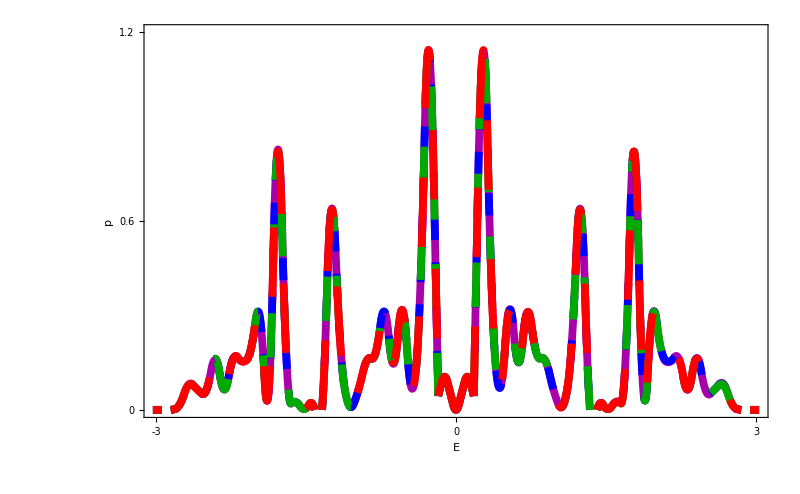

```mathematica
xrange={-3,3};
yrange={0,1.2};
Show[
ListPlot[Transpose@{n7nc4096[[1]][[;;34]],n7nc4096[[2]][[;;34]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n7nc4096[[1]][[38;;]],n7nc4096[[2]][[38;;]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n7nc4096[[1]][[34;;38]],n7nc4096[[2]][[34;;38]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n7nc4096extra[[1]],n7nc4096extra[[2]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n8nc4096[[1]][[;;34]],n8nc4096[[2]][[;;34]]},PlotStyle->{Blue,Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc4096[[1]][[38;;]],n8nc4096[[2]][[38;;]]},PlotStyle->{Blue,Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc4096[[1]][[34;;38]],n8nc4096[[2]][[34;;38]]},PlotStyle->{Blue,Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n8nc4096extra[[1]],n8nc4096extra[[2]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n9nc4096[[1]][[;;34]],n9nc4096[[2]][[;;34]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n9nc4096[[1]][[38;;]],n9nc4096[[2]][[38;;]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n9nc4096[[1]][[34;;38]],n9nc4096[[2]][[34;;38]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n9nc4096extra[[1]],n9nc4096extra[[2]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n10nc4096[[1]][[;;34]],n10nc4096[[2]][[;;34]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.08]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n10nc4096[[1]][[38;;]],n10nc4096[[2]][[38;;]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.08]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n10nc4096[[1]][[34;;38]],n10nc4096[[2]][[34;;38]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.08]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
(*ListPlot[Transpose@{n10nc4096[[1]],n10nc4096[[2]]},PlotStyle->{Red,PointSize[0.02]},PlotRange->{xrange,yrange}],*)
ListPlot[Transpose@{n10nc4096extra[[1]],n10nc4096extra[[2]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.6,1.2},None},{{-3,0, 3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
(*psize=0.05;
xrange={5.9,9.1};
yrange={0,0.0002};
Show[
ListPlot[Transpose@{{6,7,8,9},{n7nc4096[[51]],n8nc4096[[51]],n9nc4096[[51]],n10nc4096[[51]]}},PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True],
ListPlot[Transpose@{{6},{n7nc4096[[51]]}},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{7},{n8nc4096[[51]]}},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{8},{n9nc4096[[51]]}},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{9},{n10nc4096[[51]]}},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"n","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.0001,0.0002},None},{{6,7,8,9},None}},FrameTicksStyle->FontSize->50
]*)
```

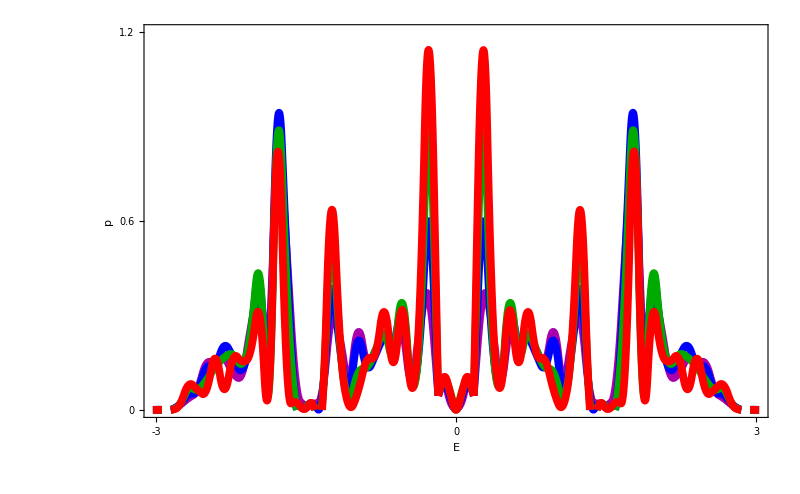

```mathematica
xrange={-3,3};
yrange={0,1.2};
Show[
ListPlot[Transpose@{n10nc512[[1]][[;;34]],n10nc512[[2]][[;;34]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n10nc512[[1]][[38;;]],n10nc512[[2]][[38;;]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n10nc512[[1]][[34;;38]],n10nc512[[2]][[34;;38]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n10nc512extra[[1]],n10nc512extra[[2]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n10nc1024[[1]][[;;34]],n10nc1024[[2]][[;;34]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n10nc1024[[1]][[38;;]],n10nc1024[[2]][[38;;]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n10nc1024[[1]][[34;;38]],n10nc1024[[2]][[34;;38]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n10nc1024extra[[1]],n10nc1024extra[[2]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n10nc2048[[1]][[;;34]],n10nc2048[[2]][[;;34]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n10nc2048[[1]][[38;;]],n10nc2048[[2]][[38;;]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n10nc2048[[1]][[34;;38]],n10nc2048[[2]][[34;;38]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n10nc2048extra[[1]],n10nc2048extra[[2]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n10nc4096[[1]][[;;34]],n10nc4096[[2]][[;;34]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n10nc4096[[1]][[38;;]],n10nc4096[[2]][[38;;]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n10nc4096[[1]][[34;;38]],n10nc4096[[2]][[34;;38]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n10nc4096extra[[1]],n10nc4096extra[[2]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.6,1.2},None},{{-3,0, 3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
(*psize=0.05;
xrange={350, 4250};
yrange={0,0.005};
Show[
ListPlot[Transpose@{{512,1024,2048,4096},{n10nc512[[51]],n10nc1024[[51]],n10nc2048[[51]],n10nc4096[[51]]}},PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True],
ListPlot[Transpose@{{512},{n10nc512[[51]]}},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{1024},{n10nc1024[[51]]}},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{2048},{n10nc2048[[51]]}},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{4096},{n10nc4096[[51]]}},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"n","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.0025,0.005},None},{{512,1024,2048,4096},None}},FrameTicksStyle->FontSize->50
]*)
```

```mathematica
datadir=StringJoin[parentdir,"/p14q3_ADOS_FullRange_71points"];
```

```mathematica
otherdatadir=StringJoin[parentdir,"/p14q3n6_StaticERange_ADOS_FullRange_71points"];
```

```mathematica
n6nc512=Import[StringJoin[otherdatadir,"/p14q3n6_Nc512_ADOS_StaticERange.txt"],"Table"];
n6nc1024=Import[StringJoin[otherdatadir,"/p14q3n6_Nc1024_ADOS_StaticERange.txt"],"Table"];
n6nc2048=Import[StringJoin[otherdatadir,"/p14q3n6_Nc2048_ADOS_StaticERange.txt"],"Table"];
n6nc4096=Import[StringJoin[otherdatadir,"/p14q3n6_Nc4096_ADOS_StaticERange.txt"],"Table"];
```

```mathematica
n7nc512=Import[StringJoin[datadir,"/p14q3n7_Nc512_ADOS.txt"],"Table"];
n7nc1024=Import[StringJoin[datadir,"/p14q3n7_Nc1024_ADOS.txt"],"Table"];
n7nc2048=Import[StringJoin[datadir,"/p14q3n7_Nc2048_ADOS.txt"],"Table"];
n7nc4096=Import[StringJoin[datadir,"/p14q3n7_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n8nc512=Import[StringJoin[datadir,"/p14q3n8_Nc512_ADOS.txt"],"Table"];
n8nc1024=Import[StringJoin[datadir,"/p14q3n8_Nc1024_ADOS.txt"],"Table"];
n8nc2048=Import[StringJoin[datadir,"/p14q3n8_Nc2048_ADOS.txt"],"Table"];
n8nc4096=Import[StringJoin[datadir,"/p14q3n8_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
extradatadir=StringJoin[parentdir,"/p14q3_ADOS_NearZeroEnergy_FillIn"];
```

```mathematica
n6nc4096extra=Import[StringJoin[extradatadir,"/p14q3n6_Nc4096_ADOS_StaticERange.txt"],"Table"];
n7nc4096extra=Import[StringJoin[extradatadir,"/p14q3n7_Nc4096_ADOS.txt"],"Table"];
n8nc4096extra=Import[StringJoin[extradatadir,"/p14q3n8_Nc4096_ADOS.txt"],"Table"];
```

```mathematica
n6nc2048extra=Import[StringJoin[extradatadir,"/p14q3n6_Nc2048_ADOS_StaticERange.txt"],"Table"];
n7nc2048extra=Import[StringJoin[extradatadir,"/p14q3n7_Nc2048_ADOS.txt"],"Table"];
n8nc2048extra=Import[StringJoin[extradatadir,"/p14q3n8_Nc2048_ADOS.txt"],"Table"];
```

```mathematica
n6nc1024extra=Import[StringJoin[extradatadir,"/p14q3n6_Nc1024_ADOS_StaticERange.txt"],"Table"];
n7nc1024extra=Import[StringJoin[extradatadir,"/p14q3n7_Nc1024_ADOS.txt"],"Table"];
n8nc1024extra=Import[StringJoin[extradatadir,"/p14q3n8_Nc1024_ADOS.txt"],"Table"];
```

```mathematica
n6nc512extra=Import[StringJoin[extradatadir,"/p14q3n6_Nc512_ADOS_StaticERange.txt"],"Table"];
n7nc512extra=Import[StringJoin[extradatadir,"/p14q3n7_Nc512_ADOS.txt"],"Table"];
n8nc512extra=Import[StringJoin[extradatadir,"/p14q3n8_Nc512_ADOS.txt"],"Table"];
```

```mathematica
n6nc4096[[1]][[35]]
n8nc4096[[1]][[37]]
```

-0.0891428571428569683

0.0891428571428574124

```mathematica
n8nc4096extra[[1]][[1]]
n8nc4096extra[[1]][[-1]]
```

-0.0891428571428569683

0.0891428571428569683

```mathematica
lthickness=0.007;
```

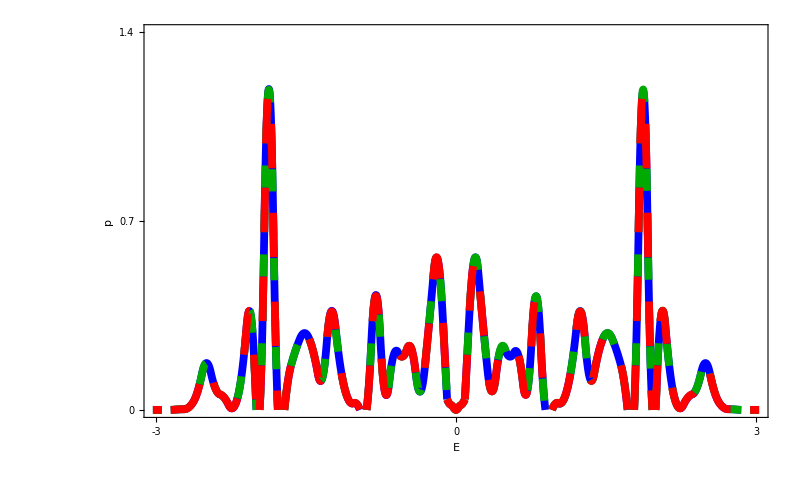

```mathematica
xrange={-3,3};
yrange={0,1.4};
Show[
ListPlot[Transpose@{n6nc4096[[1]][[;;35]],n6nc4096[[2]][[;;35]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n6nc4096[[1]][[37;;]],n6nc4096[[2]][[37;;]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n6nc4096[[1]][[34;;38]],n6nc4096[[2]][[34;;38]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n6nc4096extra[[1]],n6nc4096extra[[2]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n7nc4096[[1]][[;;35]],n7nc4096[[2]][[;;35]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n7nc4096[[1]][[37;;]],n7nc4096[[2]][[37;;]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n7nc4096[[1]][[34;;38]],n7nc4096[[2]][[34;;38]]},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n7nc4096extra[[1]],n7nc4096extra[[2]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n8nc4096[[1]][[;;35]],n8nc4096[[2]][[;;35]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc4096[[1]][[37;;]],n8nc4096[[2]][[37;;]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc4096[[1]][[34;;38]],n8nc4096[[2]][[34;;38]]},PlotStyle->{Red,Thickness[lthickness],Dashing[0.04]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
(*ListPlot[Transpose@{n8nc4096[[1]],n8nc4096[[2]]},PlotStyle->{Red,PointSize[0.02]},PlotRange->{xrange,yrange}],*)
ListPlot[Transpose@{n8nc4096extra[[1]],n8nc4096extra[[2]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.7,1.4},None},{{-3,0, 3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
(*psize=0.05;
xrange={4.9,7.1};
yrange={0,0.0003};
Show[
ListPlot[Transpose@{{5,6,7},{n6nc4096[[51]],n7nc4096[[51]],n8nc4096[[51]]}},PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True],
ListPlot[Transpose@{{5},{n6nc4096[[51]]}},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{6},{n7nc4096[[51]]}},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{7},{n8nc4096[[51]]}},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"n","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.00015,0.0003},None},{{5,6,7},None}},FrameTicksStyle->FontSize->50
]*)
```

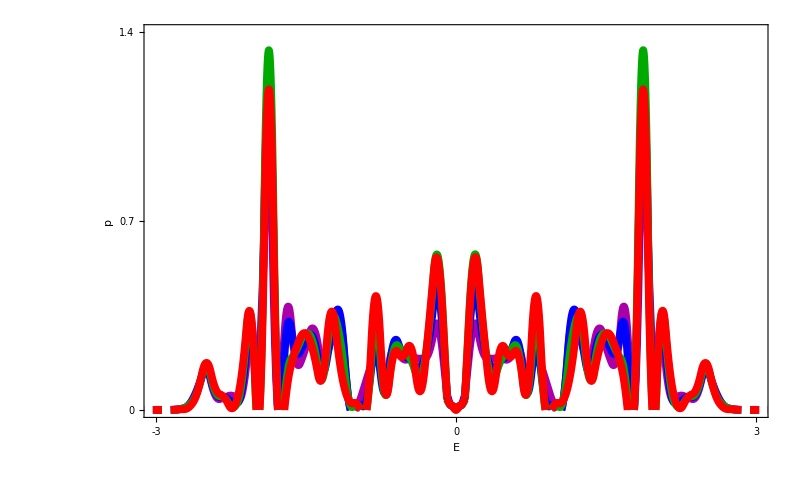

```mathematica
xrange={-3,3};
yrange={0,1.4};
Show[
ListPlot[Transpose@{n8nc512[[1]][[;;35]],n8nc512[[2]][[;;35]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc512[[1]][[37;;]],n8nc512[[2]][[37;;]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc512[[1]][[35;;37]],n8nc512[[2]][[35;;37]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n8nc512extra[[1]],n8nc512extra[[2]]},PlotStyle->{Darker[Magenta],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n8nc1024[[1]][[;;35]],n8nc1024[[2]][[;;35]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc1024[[1]][[37;;]],n8nc1024[[2]][[37;;]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc1024[[1]][[35;;37]],n8nc1024[[2]][[35;;37]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n8nc1024extra[[1]],n8nc1024extra[[2]]},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n8nc2048[[1]][[;;35]],n8nc2048[[2]][[;;35]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc2048[[1]][[37;;]],n8nc2048[[2]][[37;;]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc2048[[1]][[35;;37]],n8nc2048[[2]][[35;;37]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
ListPlot[Transpose@{n8nc2048extra[[1]],n8nc2048extra[[2]]},PlotStyle->{Darker[Green],Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

ListPlot[Transpose@{n8nc4096[[1]][[;;35]],n8nc4096[[2]][[;;35]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
ListPlot[Transpose@{n8nc4096[[1]][[37;;]],n8nc4096[[2]][[37;;]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],
(*ListPlot[Transpose@{n8nc4096[[1]][[35;;37]],n8nc4096[[2]][[35;;37]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->1],*)
(*ListPlot[Transpose@{n8nc4096[[1]],n8nc4096[[2]]},PlotStyle->{Red,PointSize[0.02]},PlotRange->{xrange,yrange}],*)
ListPlot[Transpose@{n8nc4096extra[[1]],n8nc4096extra[[2]]},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True,InterpolationOrder->2],

BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.7,1.4},None},{{-3,0, 3},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
(*psize=0.05;
xrange={350, 4250};
yrange={0,0.008};
Show[
ListPlot[Transpose@{{512,1024,2048,4096},{n8nc512[[51]],n8nc1024[[51]],n8nc2048[[51]],n8nc4096[[51]]}},PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange},Joined->True],
ListPlot[Transpose@{{512},{n8nc512[[51]]}},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{1024},{n8nc1024[[51]]}},PlotStyle->{Blue,PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{2048},{n8nc2048[[51]]}},PlotStyle->{Darker[Green],PointSize[psize]},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{4096},{n8nc4096[[51]]}},PlotStyle->{Red,PointSize[psize]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"n","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.004,0.008},None},{{512,1024,2048,4096},None}},FrameTicksStyle->FontSize->50
]*)
```

## With Magnetic Field

```mathematica
datadir="../Processed_Data/11_Appendix_KPM_DOS/With_Magnetic_Field_Hermitian";
```

```mathematica
nhdatadir="../Processed_Data/11_Appendix_KPM_DOS/With_Magnetic_Field_NH";
```

```mathematica
p10beta0=Import[StringJoin[datadir,"/p10q3n9_beta0_16384moments_calculateADOSvalues.txt"],"Table"];
p10beta0d92=Import[StringJoin[datadir,"/p10q3n9_beta0.92_16384moments_calculateADOSvalues.txt"],"Table"];
p10beta0d94=Import[StringJoin[datadir,"/p10q3n9_beta0.94_16384moments_calculateADOSvalues.txt"],"Table"];
p10beta1=Import[StringJoin[datadir,"/p10q3n9_beta1.0_16384moments_calculateADOSvalues.txt"],"Table"];
```

```mathematica
p14beta0=Import[StringJoin[datadir,"/p14q3n7_beta0_16384moments_calculateADOSvalues.txt"],"Table"];
p14beta0d92=Import[StringJoin[datadir,"/p14q3n7_beta0.92_16384moments_calculateADOSvalues.txt"],"Table"];
p14beta0d94=Import[StringJoin[datadir,"/p14q3n7_beta0.94_16384moments_calculateADOSvalues.txt"],"Table"];
p14beta1=Import[StringJoin[datadir,"/p14q3n7_beta1.0_16384moments_calculateADOSvalues.txt"],"Table"];
```

```mathematica
p10a0d4beta1=Import[StringJoin[nhdatadir,"/p10q3n9a0d4_beta1_16384moments_calculateADOSvalues.txt"],"Table"];
p10a0d8beta1=Import[StringJoin[nhdatadir,"/p10q3n9a0d8_beta1_16384moments_calculateADOSvalues.txt"],"Table"];
p14a0d4beta1=Import[StringJoin[nhdatadir,"/p14q3n7a0d4_beta1_16384moments_calculateADOSvalues.txt"],"Table"];
p14a0d8beta1=Import[StringJoin[nhdatadir,"/p14q3n7a0d8_beta1_16384moments_calculateADOSvalues.txt"],"Table"];
```

```mathematica
linethickness=0.006;
```

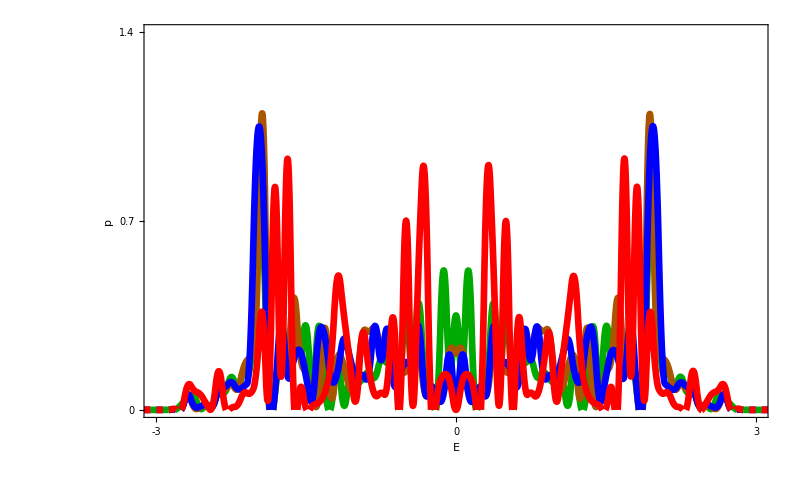

```mathematica
xrange={-3,3};
yrange={0,1.4};
Show[
ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0d94[[1]],p10beta0d94[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Orange],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0d92[[1]],p10beta0d92[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0[[1]],p10beta0[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.7,1.4},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

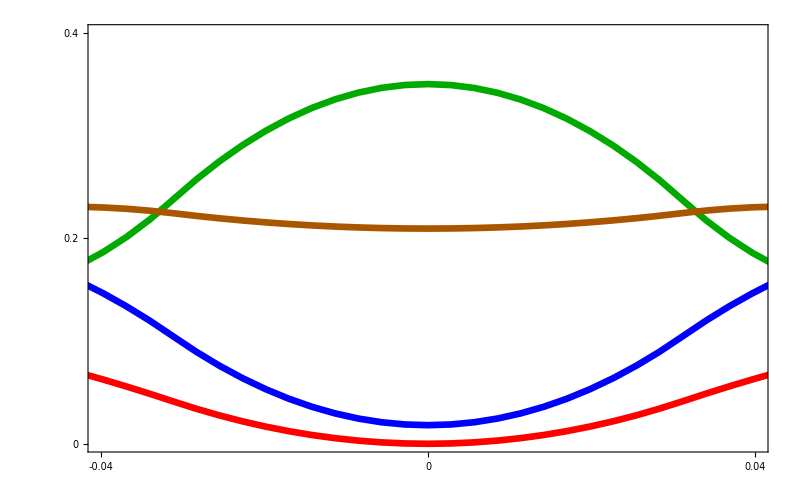

```mathematica
xrange={-0.04,0.04};
yrange={0,0.4};
Show[
ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0d94[[1]],p10beta0d94[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Orange],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0d92[[1]],p10beta0d92[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta0[[1]],p10beta0[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.04,0,0.04},None}},FrameTicksStyle->FontSize->50
]
```

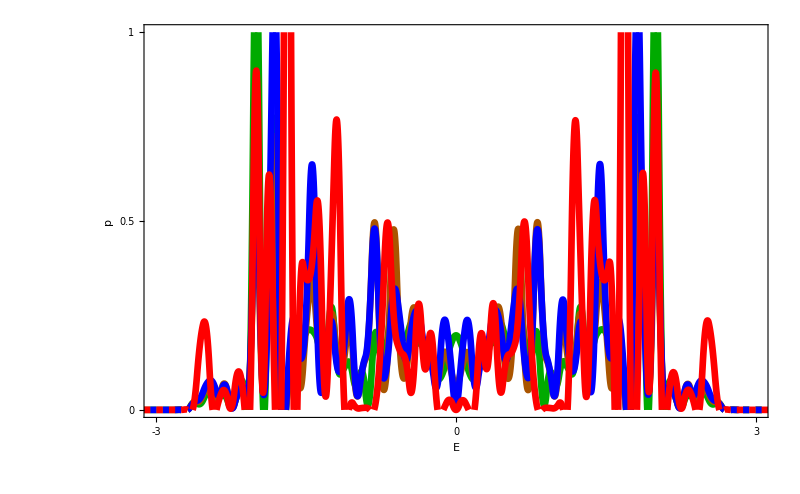

```mathematica
xrange={-3,3};
yrange={0,1};
Show[
ListPlot[Transpose@{p14beta1[[1]],p14beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0d94[[1]],p14beta0d94[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Orange],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0d92[[1]],p14beta0d92[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0[[1]],p14beta0[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

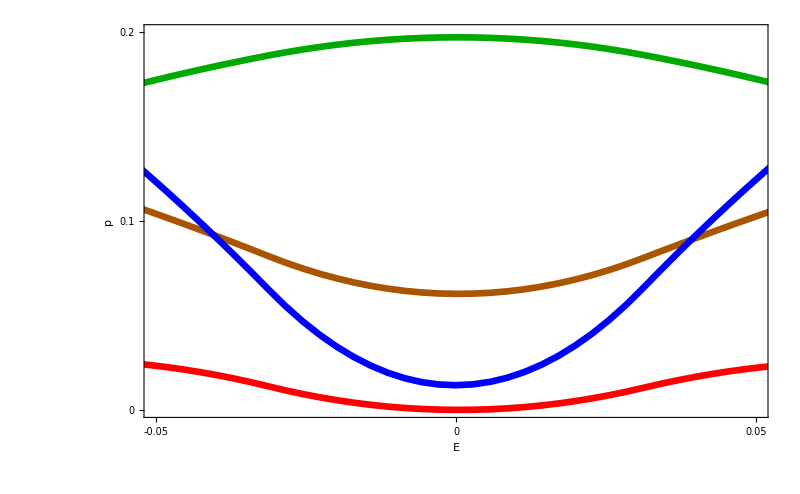

```mathematica
xrange={-0.05,0.05};
yrange={0,0.2};
Show[
ListPlot[Transpose@{p14beta1[[1]],p14beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0d94[[1]],p14beta0d94[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Orange],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0d92[[1]],p14beta0d92[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta0[[1]],p14beta0[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.1,0.2},None},{{-0.05,0,0.05},None}},FrameTicksStyle->FontSize->50
]
```

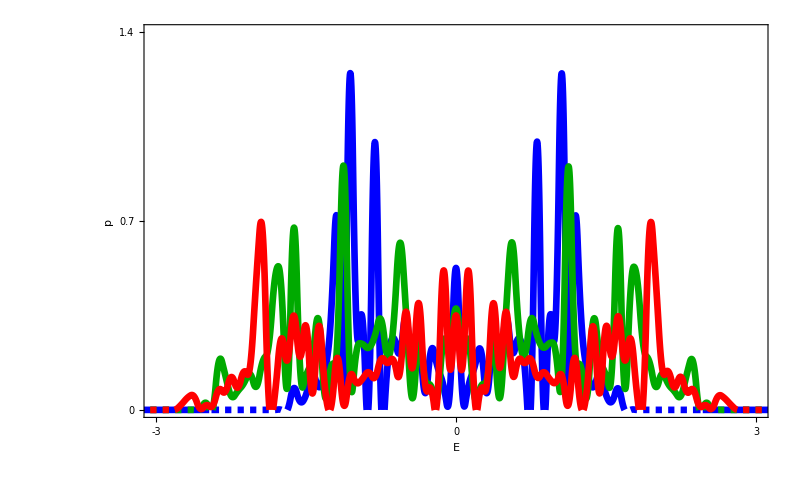

```mathematica
xrange={-3,3};
yrange={0,1.4};
Show[
ListPlot[Transpose@{p10a0d8beta1[[1]],p10a0d8beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10a0d4beta1[[1]],p10a0d4beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],
(*ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},PlotStyle->{Red,PointSize[0.02]},PlotRange->{xrange,yrange}],*)


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.7,1.4},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

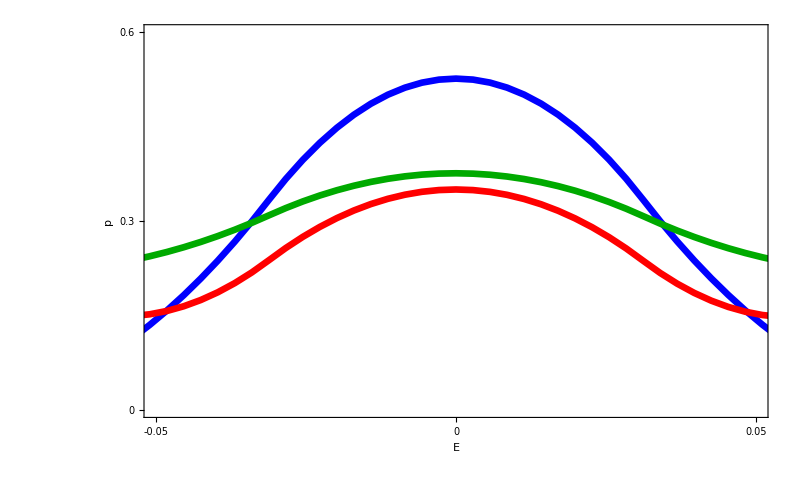

```mathematica
xrange={-0.05,0.05};
yrange={0,0.6};
Show[
ListPlot[Transpose@{p10a0d8beta1[[1]],p10a0d8beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10a0d4beta1[[1]],p10a0d4beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],
(*ListPlot[Transpose@{p10beta1[[1]],p10beta1[[2]]},PlotStyle->{Red,PointSize[0.02]},PlotRange->{xrange,yrange}],*)


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.3,0.6},None},{{-0.05,0,0.05},None}},FrameTicksStyle->FontSize->50
]
```

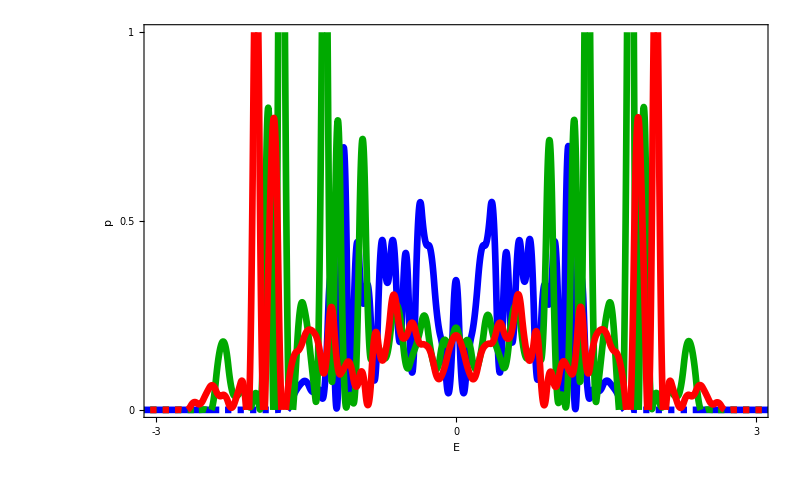

```mathematica
xrange={-3,3};
yrange={0,1};
Show[
ListPlot[Transpose@{p14a0d8beta1[[1]],p14a0d8beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14a0d4beta1[[1]],p14a0d4beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta1[[1]],p14beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

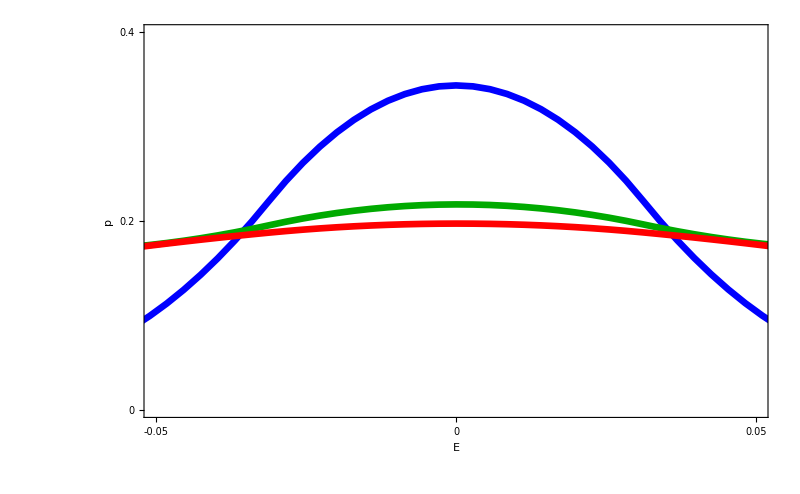

```mathematica
xrange={-0.05,0.05};
yrange={0,0.4};
Show[
ListPlot[Transpose@{p14a0d8beta1[[1]],p14a0d8beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Blue,Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14a0d4beta1[[1]],p14a0d4beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Green],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{p14beta1[[1]],p14beta1[[2]]},Joined->True,InterpolationOrder->2,PlotStyle->{Red,Thickness->linethickness},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"E","p"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.05,0,0.05},None}},FrameTicksStyle->FontSize->50
]
```